```mathematica
all=Import["/home/dkoslicki/Dropbox/AllPapers/Abstracts.txt"];
```

```mathematica
(*first few pages
all=Import["/home/dkoslicki/Dropbox/AllPapers/Extracted_text2.txt"];
```

```mathematica
(*every single page*)
all=Import["/home/dkoslicki/Dropbox/AllPapers/Extracted_text3.txt"];
```

```mathematica
StringLength[all]
```

102252

```mathematica
Thread[Characters["0123456789"]->""]
```

{0→,1→,2→,3→,4→,5→,6→,7→,8→,9→}

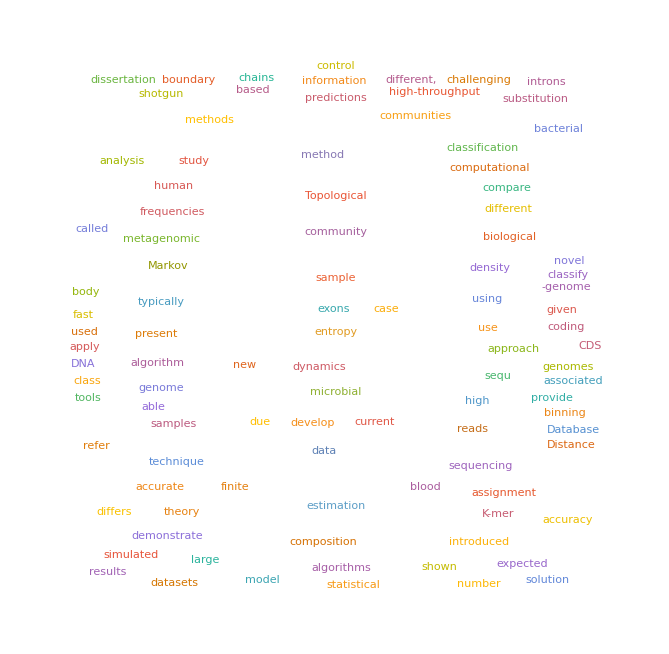

```mathematica
WordCloud[clean=DeleteCases[DeleteCases[DeleteCases[StringSplit[StringReplace[StringReplace[DeleteCases[DeleteStopwords[all],x_/;StringLength[x]≤2],{"\\"->"","et al."->"","preprint"->"","["->"",".:}"->"","]"->"","."->"",":"->"","{"->"","}"->"","peer"->"","reviewed"->"",")"->"","("->"","microbiomeome"->"microbiome","/"->"","funder"->"","internation"->"","taxonomic"->"",","->""}],Thread[Characters["0123456789"]->""]]],x_/;MemberQ[x,{"reence","license","internation","Germany","microbiomeome","difent"}]],x_/;Or[Not[StringFreeQ[x,","]],MemberQ[{"holder","M,","-,","e,","bioinv","BP","al"},x]]],x_/;StringLength[x]≤1]]
```

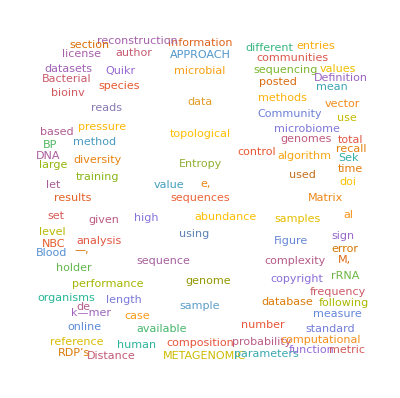

```mathematica
WordCloud[clean=DeleteCases[DeleteCases[StringSplit[StringReplace[StringReplace[DeleteCases[DeleteStopwords[all],x_/;StringLength[x]≤2],{"\\"->"","et al."->"","preprint"->"","["->"",".:}"->"","]"->"","."->"",":"->"","{"->"","}"->"","peer"->"","reviewed"->"",")"->"","("->"","microbiomeome"->"microbiome","/"->"","funder"->"","internation"->"","taxonomic"->""}],Thread[Characters["0123456789"]->""]]],x_/;MemberQ[x,{"reence","license","internation","Germany","microbiomeome","difent"}]],x_/;StringLength[x]≤1]]
```

```mathematica
piCurve[t_]=(WolframAlpha["pi curve",{{"EquationsPod:PopularCurveData",1},"ComputableData"}]/. _ == xy_  :> xy /. Hold -> Identity)/(* rescale*)600;
```

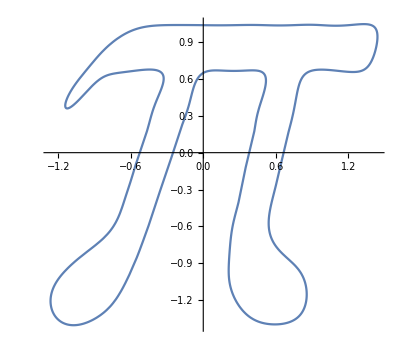

```mathematica
im1=ParametricPlot[piCurve[t],{t,0,2π}]
```

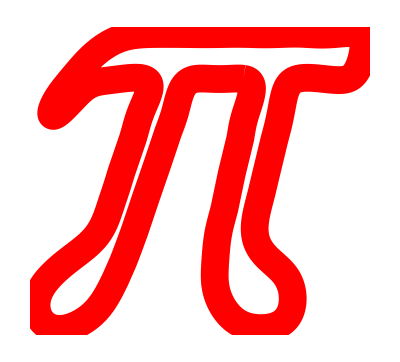

```mathematica
im1=ParametricPlot[piCurve[t],{t,0,2π},Axes->False,PlotStyle->{Thickness[.05],Red}]
```

```mathematica
FillingTransform[im1]
```

-Graphics-

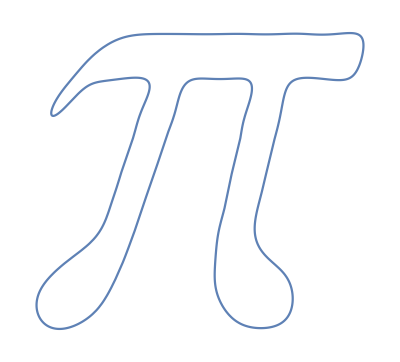

```mathematica
im2=ParametricPlot[piCurve[t],{t,0,2π},Axes->False]
```

```mathematica
WordCloud[clean,-Graphics-]
```

$Aborted

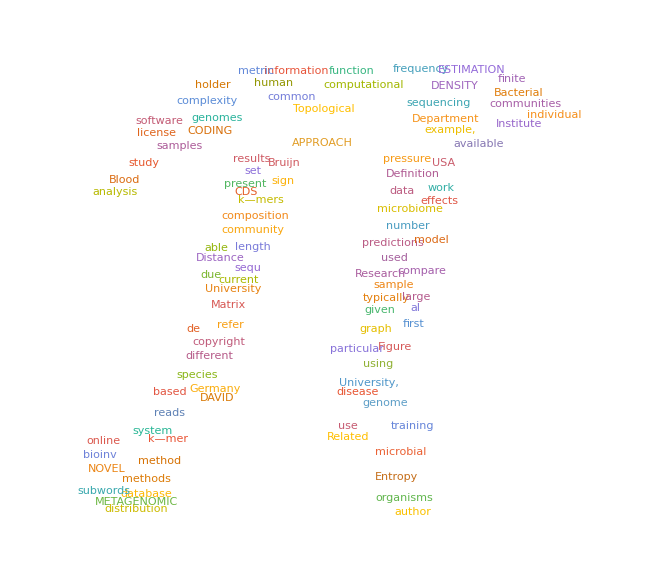

```mathematica
WordCloud[clean,-Graphics-]
```

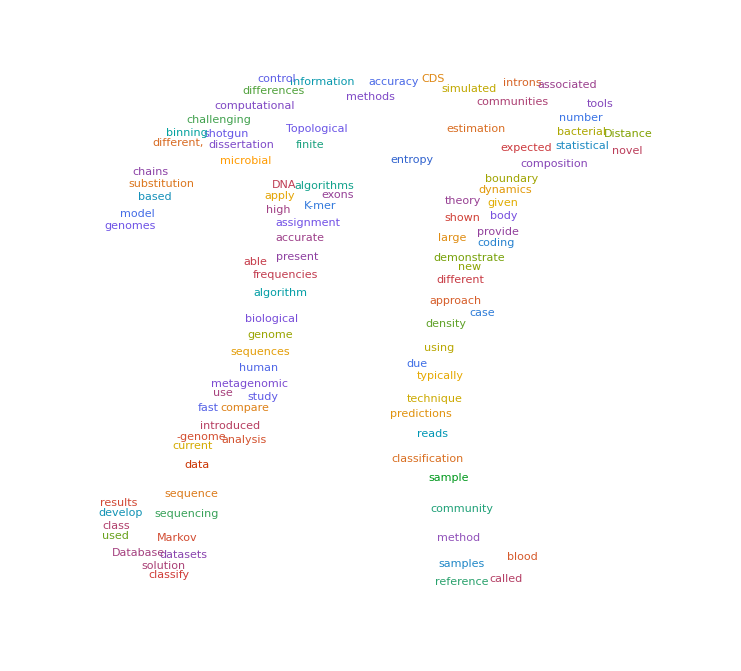

```mathematica
WordCloud[clean,-Graphics-,PlotTheme->"Web"]
```

```mathematica
text=First[First[ImportString[ExportString[Style["MATH",Italic,FontSize->40,FontFamily->"Times"],"PDF"],"PDF","TextMode"->"Outlines"]]];
```

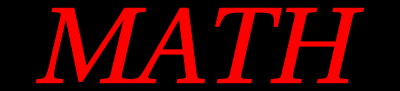

```mathematica
graphic=Graphics[{EdgeForm[Directive[Red,Thick]],Red,text},Background->Black,PlotRange->Automatic]
```

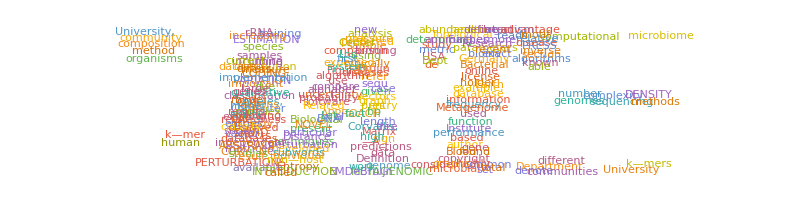

```mathematica
WordCloud[clean,graphic,MaxItems->200]
```

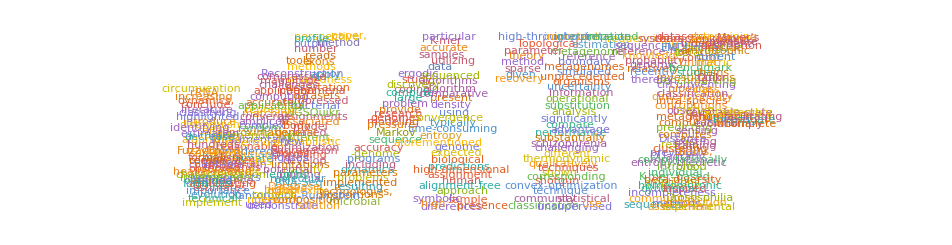

```mathematica
WordCloud[clean,graphic,MaxItems->600]
```

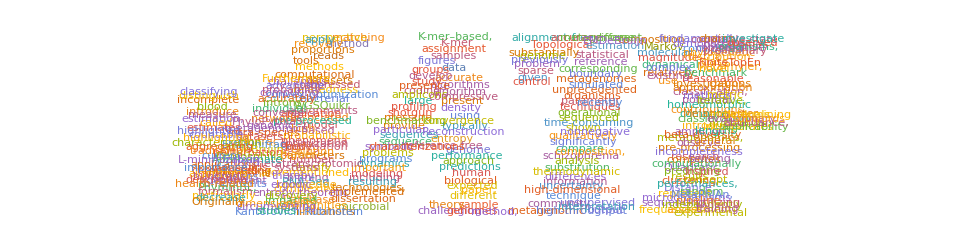

```mathematica
WordCloud[clean,graphic,MaxItems->700,ScalingFunctions->Log]
```

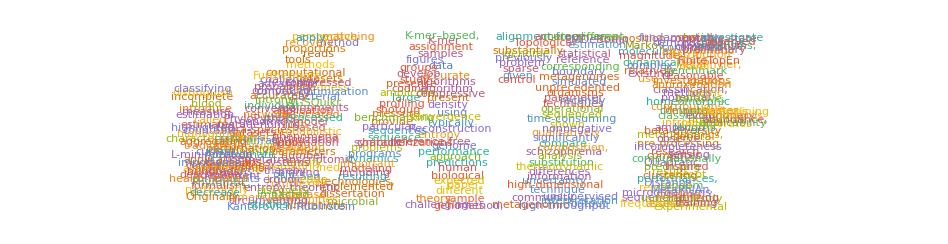

```mathematica
WordCloud[clean,graphic,MaxItems->700,ScalingFunctions->{(#^2)&}]
```

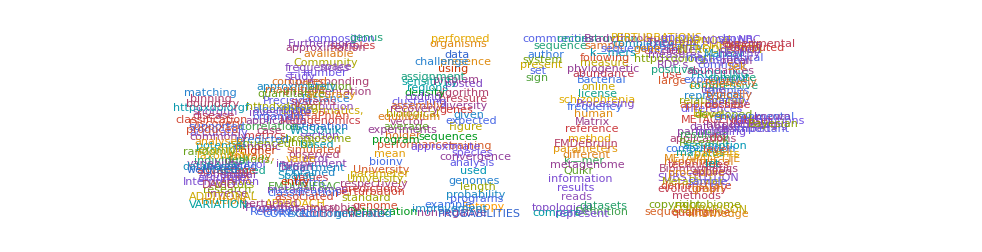

```mathematica
out=WordCloud[clean,graphic,MaxItems->700,ScalingFunctions->{(#^.5)&},PlotTheme->"Web"]
```

```mathematica
Export["/home/dkoslicki/Dropbox/AllPapers/WebsiteWordCloud.png",out,ImageSize->{1100,284},ImageResolution->400]
```

/home/dkoslicki/Dropbox/AllPapers/WebsiteWordCloud.png

```mathematica
Export["/home/dkoslicki/Dropbox/AllPapers/WebsiteWordCloudBig.png",out,ImageSize->{1100*1.4,284*1.4},ImageResolution->600]
```

/home/dkoslicki/Dropbox/AllPapers/WebsiteWordCloudBig.png

```mathematica
Export["/home/dkoslicki/Dropbox/AllPapers/WebsiteWordCloud.pdf",out,ImageSize->{1100,284}]
```

/home/dkoslicki/Dropbox/AllPapers/WebsiteWordCloud.pdf

```mathematica
Export["/home/dkoslicki/Dropbox/AllPapers/WebsiteWordCloud.jpeg",out,ImageSize->{1100,284},ImageResolution->400]
```

/home/dkoslicki/Dropbox/AllPapers/WebsiteWordCloud.jpeg

```mathematica
Length[clean]
```

8341

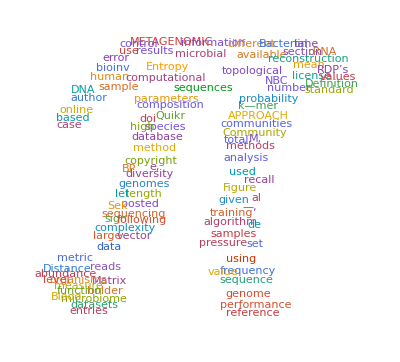

```mathematica
piout=WordCloud[clean,-Graphics-,PlotTheme->"Web"]
```

```mathematica
Export["/home/dkoslicki/Dropbox/AllPapers/WebsiteWordCloudBigPi.png",piout,ImageSize->{1100*1.4,284*1.4},ImageResolution->600]
```

/home/dkoslicki/Dropbox/AllPapers/WebsiteWordCloudBigPi.png